## PHSX 565 Astrophysical Plasma Physics Problem Set 5 - Force-free Magnetic Fields Roy Smart

### Prepare Mathematica environment

#### Clear variables

```mathematica
Clear["Global`*"]
vals = {};
```

#### Define shortcut to convert rule to equation

```mathematica
r2e = Rule -> Equal;
```

#### Use preprint variable to print derivatives in traditional form

```mathematica
$PrePrint=#/.Derivative[id__][f_][args__]:>TraditionalForm[HoldForm@D[f[args],#]&[Sequence@@(DeleteCases[Transpose[{{args},{id}}],{_,0}]/.{x_,1}:>x)]]&;
(*$PrePrint = TraditionalForm*)
```

#### Define the del operator

```mathematica
$x = {x,y,z};
▽/:▽ f_:=Grad[f,$x]
▽·f_:=Div[f,$x]
▽/:▽×f_:=Curl[f,$x]
▽·▽:=Δ
▽/:▽^2:=Δ
Δ/:Δ f_:=Laplacian[f,$x]
CenterDot/:(v_·▽) f_:=Grad[f,$x].v
```

## Part a.

### Find the constant-α field

#### We are given the following boundary conditions in the Problem Statement.

```mathematica
bc1 = Bz[y,0] ->  B0 Cos[π/L y];
bc2 = Bz[y,2L]->  0;
bc3 = By[-L,z] ->  0;
bc4 = By[L,z] ->  0;
```

```mathematica
$Assumptions = B0 > 0;
```

#### Constant-α force-free fields with cartesian symmetry and boundary conditions are solutions to Longcope 10.41, given as

```mathematica
f$a[y_,z_] := f[y,z]->B1 Sin[k y] Cos[√(α^2 - k^2) z] ;
$Assumptions = $Assumptions &&  α ≥  π/L && y ≥ -L && y ≤ L && z ≥ 0 && z ≤ 2L;
```

#### Where C0 is a unknown constant and the wavenumber, k, is

```mathematica
k$a = k-> π/L;
```

```mathematica
$Assumptions = $Assumptions && L > 0;
```

#### The magnetic field can be calculated through Longcope 10.27

```mathematica
B$a[y_,z_] = B[y,z]-> (▽ (f[y,z] /. f$a[y,z])) × (▽ x)
```

B[y,z]→{0,-B1 √(-k^2+α^2) Sin[k y] Sin[z √(-k^2+α^2)],-B1 k Cos[k y] Cos[z √(-k^2+α^2)]}

#### Which is a solution to the Helmholtz equation, Longcope 10.41

```mathematica
$1041 = Δ f[y,z] ==- α^2 f[y,z]
```

(∂^2 f(y,z))/(∂y^2)+(∂^2 f(y,z))/(∂z^2)==-α^2 f[y,z]

#### Use the boundary conditions to find the constants C0 and α

```mathematica
e1$a = Bz[y,0] == B$a[y,0][[2,3]];
e2$a = Bz[y,2L] ==  B$a[y,2 L][[2,3]];
e3$a = By[-L,z] ==  B$a[-L,z][[2,2]];
e4$a = By[L,z] ==  B$a[L,z][[2,2]];
```

```mathematica
$Assumptions = $Assumptions && n∈Integers;
{{B1$a, α$a1},{B1$a, α$a2}} = (Solve[Reduce[{e1$a /. bc1 , e2$a /. bc2, e3$a /. bc3, e4$a /. bc4} /. k$a] /. C[1]-> n//FullSimplify,{B1,α}] //FullSimplify //Quiet);
```

```mathematica
B1$a
α$a1
α$a2
```

B1→-(B0 L)/π

α→(√(17+8 n (-1+2 n)) π)/(4 L)

α→(√(17+8 n (1+2 n)) π)/(4 L)

#### Plug constants into solution

```mathematica
(f$a1 = f$a[y,z] /. B1$a /. α$a1 /. k$a //FullSimplify) //Framed
(f$a2 = f$a[y,z] /. B1$a /. α$a2 /. k$a //FullSimplify) //Framed
```

f[y,z]→-(B0 L Cos[((1-4 n) π z)/(4 L)] Sin[(π y)/L])/π

f[y,z]→-(B0 L Cos[((1+4 n) π z)/(4 L)] Sin[(π y)/L])/π

#### Evaluate magnetic field

```mathematica
B$a1[y_,z_] = B$a[y,z]/. B1$a /. α$a1 /. k$a //FullSimplify
B$a2[y_,z_] = B$a[y,z]/. B1$a /. α$a2 /. k$a //FullSimplify
```

B[y,z]→{0,1/4 B0 (1-4 n) Sin[(π y)/L] Sin[((1-4 n) π z)/(4 L)],B0 Cos[(π y)/L] Cos[((1-4 n) π z)/(4 L)]}

B[y,z]→{0,1/4 B0 (1+4 n) Sin[(π y)/L] Sin[((1+4 n) π z)/(4 L)],B0 Cos[(π y)/L] Cos[((1+4 n) π z)/(4 L)]}

#### Plot solution

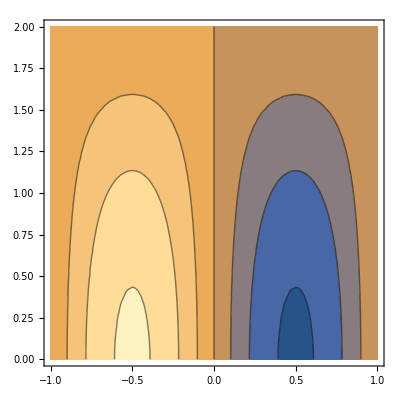

```mathematica
ContourPlot[f$a1[[2]]/. B0 -> 1 /. L-> 1 /. n-> 0,{y,-1,1},{z,0,2}]
```

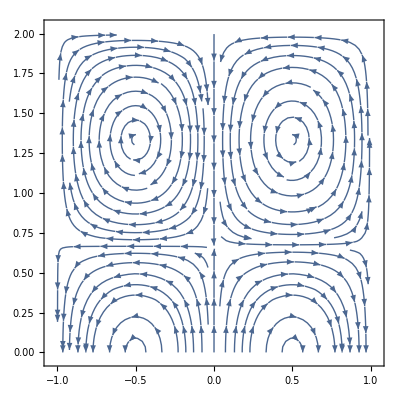

```mathematica
StreamPlot[(B$a1[y,z][[2]]/. B0 -> 1 /. L-> 1 /. n-> 1)[[2;;3]],{y,-1,1},{z,0,2}]
```

## Part b.

### Compute the magnetic energy per unit length

#### The magnetic energy is calculated using Longcope 8.21

```mathematica
n$b = Solve[α$a2/. r2e,n][[1]];
(EM$b =EM->( 1/(8 π)Integrate[B[y,z].B[y,z]/. B$a[y,z] /. B1$a /. k$a ,{y,-L,L},{z,0,2L}] /. α$a2 //FullSimplify ) /. n$b //FullSimplify)//Framed
```

EM→(B0^2 L^4 α^2)/(8 π^3)

## Part c.

### Find the field line

#### The magnetic field line has the boundary conditions

```mathematica
bc$c = z[L/2+ε] == 0;
$Assumptions = $Assumptions && ε>0&& ε < L;
```

#### A magnetic field line satisfies Longcope 9.1

```mathematica
$91y = D[y[s], s] == B[y[s],z[s]].(▽ y)
$91z = D[z[s], s] == B[y[s],z[s]].(▽ z)
```

(∂y(s))/(∂s)==B[y[s],z[s]].{0,1,0}

(∂z(s))/(∂s)==B[y[s],z[s]].{0,0,1}

#### Form a ratio of the coupled differential equations

```mathematica
eq$c =D[z[y],y] == (B$a1[y,z[y]][[2,3]])/(B$a1[y,z[y]][[2,2]])
```

(∂z(y))/(∂y)==(4 Cot[(π y)/L] Cot[((1-4 n) π z[y])/(4 L)])/(1-4 n)

#### Solve the ODE for z as a function of y

```mathematica
{z$c1,z$c2} = DSolve[{eq$c,bc$c},z[y],y][[;;,1]];
z$c1 
z$c2
```

z[y]→-(4 L ArcCos[Csc[(π y)/L] Sin[(π (L/2+ε))/L]])/((-1+4 n) π)

z[y]→(4 L ArcCos[Csc[(π y)/L] Sin[(π (L/2+ε))/L]])/((-1+4 n) π)

#### Expand for ε << L

```mathematica
zA$c1= z[y]-> Series[z$c1[[2]],{ε,0,2}] //Normal //Simplify
zA$c2= z[y]-> Series[z$c2[[2]],{ε,0,2}] //Normal //Simplify
```

z[y]→(-4 L^2 ArcCos[Csc[(π y)/L]]-(2 π^2 ε^2 Csc[(π y)/L])/(√(1-Csc[(π y)/L]^2)))/(-L π+4 L n π)

z[y]→(4 L^2 ArcCos[Csc[(π y)/L]]+(2 π^2 ε^2 Csc[(π y)/L])/(√(1-Csc[(π y)/L]^2)))/(-L π+4 L n π)

### How does the location of the other footpoint vary with α?

#### Set expression above and solve for y.

```mathematica
{z0$c1,z0$c2 }=FullSimplify[Solve[z$c1[[2]] == 0,y],Assumptions->C[1]==0][[;;,1]]
```

{y→L-(L ArcSin[Cos[(π ε)/L]])/π,y→(L ArcSin[Cos[(π ε)/L]])/π}

#### We find that the results are independent of α

```mathematica
(z0$c1= y-> Series[z0$c1[[2]],{ε,0,1}] //Normal) //Framed
(z0$c2 = y-> Series[z0$c2[[2]],{ε,0,1}] //Normal)//Framed
```

y→L/2+ε

y→L/2-ε

### How does the apex vary with α?

#### Set the derivative equal to zero and solve for the y-value

```mathematica
dz0$c = Solve[D[z$c1[[2]],y] == 0,y][[2,1]]
```

y→L/2

#### Plug in y-value to find height

```mathematica
zL$c = z$c1 /. dz0$c /. n$b //FullSimplify //Framed
```

z[L/2]→(2 π ε)/(π+2 √(-π^2+L^2 α^2))

## Part d.

### Find solutions with homogenous boundary conditions

#### Homogenous boundary conditions

```mathematica
bc1$d = Bz[y,0] ->  0;
bc2$d = Bz[y,2L]->  0;
bc3$d = By[-L,z] ->  0;
bc4$d = By[L,z] ->  0;
```

#### Propose flux function solution

```mathematica
f$d[y_,z_] := f[y,z]->B1 Sin[k y] Sin[√(α^2 - k^2) z] ;
```

#### Evaluate magnetic field

```mathematica
B$d[y_,z_] = B[y,z]-> (▽ (f[y,z] /. f$d[y,z])) × (▽ x)
```

B[y,z]→{0,B1 √(-k^2+α^2) Cos[z √(-k^2+α^2)] Sin[k y],-B1 k Cos[k y] Sin[z √(-k^2+α^2)]}

#### Use the boundary conditions to find the constants C0 and α

```mathematica
e1$d = Bz[y,0] == B$d[y,0][[2,3]];
e2$d = Bz[y,2L] ==  B$d[y,2 L][[2,3]];
e3$d = By[-L,z] ==  B$d[-L,z][[2,2]];
e4$d = By[L,z] ==  B$d[L,z][[2,2]];
```

```mathematica
$Assumptions = $Assumptions && n∈Integers;
(Solve[Reduce[{e1$d /. bc1$d , e2$d /. bc2$d, e3$d /. bc3$d, e4$d /. bc4$d} /. k$a] /. C[1]-> n//FullSimplify,{B1,α}] //FullSimplify //Quiet)
```

{{}}

```mathematica
B1$d
α$d1
α$d2
```

B1$d

α$d1

α$d2

```mathematica
Solve[Reduce[{e1$d /. bc1$d , e2$d /. bc2$d, e3$d /. bc3$d, e4$d /. bc4$d} /. k$a]/. C[1]-> n//FullSimplify,α]
```

{{}}

```mathematica
{e1$d /. bc1$d , e2$d /. bc2$d, e3$d /. bc3$d, e4$d /. bc4$d} /. k$a
```

{True,0==-(B1 π Cos[(π y)/L] Sin[2 L √(-π^2/L^2+α^2)])/L,True,True}

```mathematica
Reduce[e2$d /. bc2$d/. k$a,α]/. C[1]-> n//FullSimplify
```

B1==0||4 L n==L+2 y||L+4 L n==2 y||(n==Abs[n]&&√(1+n^2) π==L α)||(Sign[1+2 n]==1&&√(5+4 n (1+n)) π==2 L α)

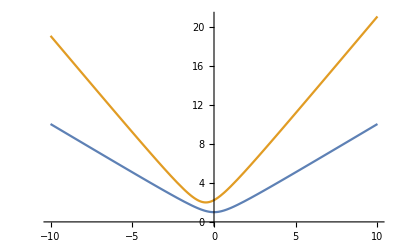

```mathematica
Plot[{√(1+n^2),√(5+4 n (1+n))},{n,-10,10}]
```